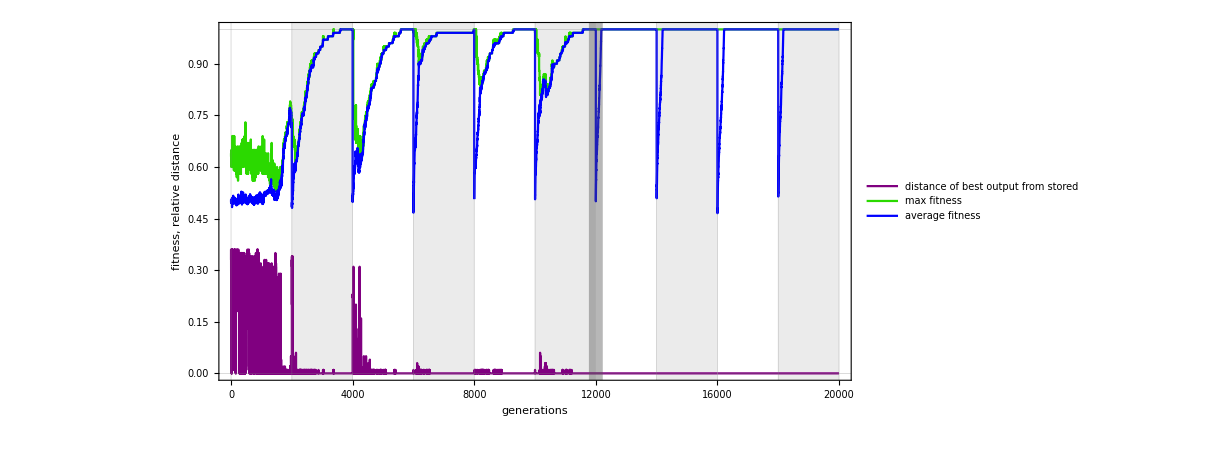

Save figure

```mathematica
(* By István Zachar *)
(* istvan.zachar80@gmail.com *)
(* 2016 *)
(* Mathematica 11.0.0.0 *)

{storemax,maxtrainT,envlen}={1000,12000,2000};
dir=NotebookDirectory[];
name="envchange";
colors={RGBColor[0.5, 0, 0.5],Hue[0.3, 1., 0.85],RGBColor[0, 0, 1]};

file=FirstCase[FileNames["*.dat",dir],_];
data=Import[file,"Table"];
{times,maxw,avgw,dist}={data[[All,1]],data[[All,2]],data[[All,3]],data[[All,6]]};
maxt=Max@times;
plot=ListPlot[{Most[{times,dist}ᵀ],Most[{times,maxw}ᵀ],Most[{times,avgw}ᵀ]},
Joined->{True,True,True},
PlotStyle->colors,
Prolog->{{GrayLevel@.92,Rectangle[{#*envlen,-1},{(#+1)*envlen,2}]}&/@Range[1,20,2]},
PlotRange->{{0,maxt},{-.0,1}},PlotRangePadding->{Scaled@0.015,Scaled@.03},
GridLines->{Range[0,maxt,envlen]/.maxtrainT->{maxtrainT,Directive[GrayLevel@.3,AbsoluteThickness@10]},{0,1}},
PlotLegends->Placed[LineLegend[Directive[#,Thick]&/@colors,Style[#,16]&/@{"distance of best output from stored","max fitness","average fitness"},LegendLayout->(Panel@Grid[##,Alignment->Left]&)],Scaled@{.8,.2}],
ImageSize->900,AspectRatio->1/2,PlotTheme->"Scientific",Background->White,
LabelStyle->{Black,16},
FrameLabel->{"generations","fitness, relative distance"},FrameStyle->Black,FrameTicks->{{Automatic,Automatic},{Range[0,30000,2000],Automatic}}]

Panel@Column@{
InputField[Dynamic@name,String],
Button["Save figure",Export[FileNameJoin@{dir,name<>".tiff"},plot,"TIFF",ImageResolution->600,"ImageEncoding"->"LZW","CompressionLevel"->1]]
}
```